#### Design

```mathematica
utm[θ_]:=√3 Cos[θ/2];
```

```mathematica
utm[Pi/6]
```

1/2 √(3/2) (1+√3)

```mathematica
vtm[θ_]:=2 √(2/(5-3 Cos[θ]));
```

```mathematica
vtm[Pi/6]
```

2 √(2/(5-(3 √3)/2))

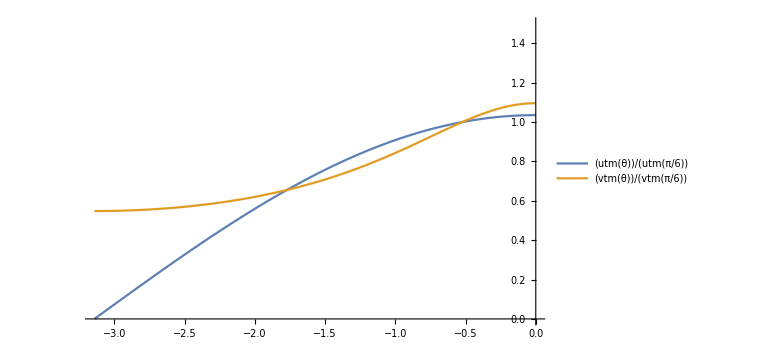

```mathematica
Plot[{utm[θ]/utm[Pi/6],vtm[θ]/vtm[Pi/6]},{θ,-Pi,0},ImageSize->Large,PlotLegends->"Expressions",PlotRange->{{-Pi,0},{0,1.5}}]
```

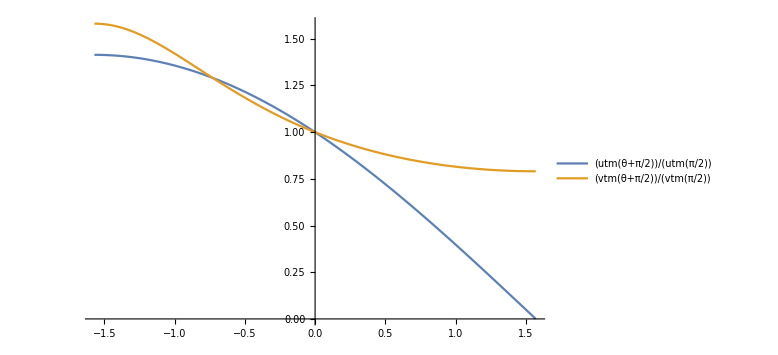

```mathematica
Plot[{utm[θ+Pi/2]/utm[Pi/2],vtm[θ+Pi/2]/vtm[Pi/2]},{θ,-Pi/2,Pi/2},ImageSize->Large,PlotLegends->"Expressions"]
```

#### Linear solution

```mathematica
ϕ=Pi/6;
```

```mathematica
ulim=Pi-ϕ
```

(5 π)/6

```mathematica
N[ulim]
```

2.61799

```mathematica
NumberForm[2.6179938779914944,16]
```

2.617993877991494

```mathematica
d3=0.1;c1=5;
```

```mathematica
A={{utm[θ+ϕ]/utm[ϕ],0},{0,vtm[θ+ϕ]/vtm[ϕ]}};
```

```mathematica
Cp=D[Transpose[A].A,θ];
```

```mathematica
Cpp=D[Transpose[A].A,{θ,2}];
```

```mathematica
J = Sqrt[Det[Aᵀ.A]];
```

```mathematica
g=Tr[Cpᵀ.Cp];
gp=D[g,θ];
```

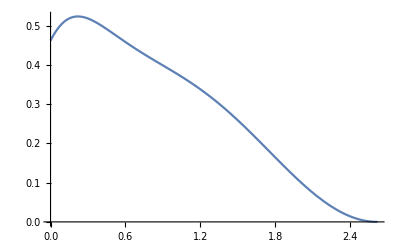

```mathematica
Plot[g,{θ,0,ulim}]
```

```mathematica
(*Plot[{θ A[[1,1]] *Cp[[1,1]]/(Cp[[1,1]]^2+Cp[[2,2]]^2),θ A[[2,2]] *Cp[[2,2]]/(Cp[[1,1]]^2+Cp[[2,2]]^2)},{θ,0,Pi-ϕ},ImageSize->Large,PlotLegends->"Expressions"]*)
```

```mathematica
dt=-d3*θ*J/(c1 g + d3 J);
```

```mathematica
P=4 c1 A.Cp*θ/(c1 g + d3 J);
```

```mathematica
(*Plot[{P[[1,1]],P[[2,2]],Norm[P,"Frobenius"]},{θ,0,1.5},ImageSize->Large,PlotLegends->"Expressions"]*)
```

```mathematica
(*ParametricPlot[{-(utm[θ+ϕ]-utm[ϕ])/utm[ϕ],P[[1,1]]},{θ,0,Pi-ϕ}]*)
```

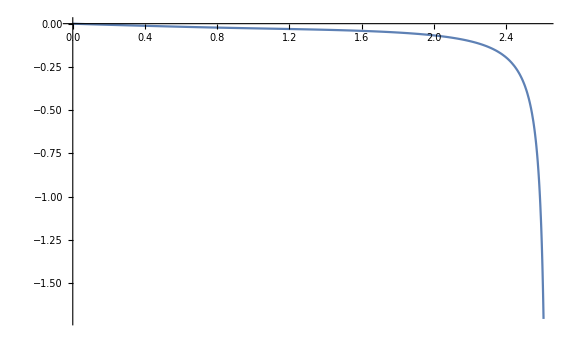

```mathematica
Plot[dt,{θ,0,ulim-0.01},ImageSize->Large,PlotLegends->"Expressions",PlotRange->All]
```

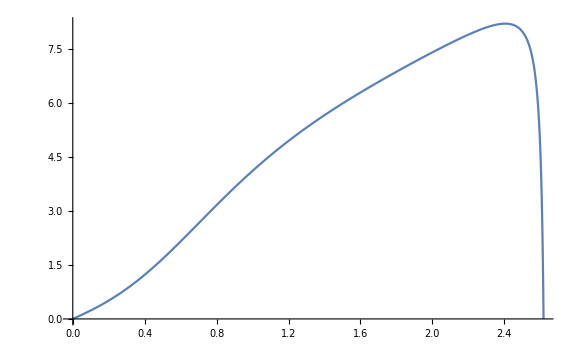

```mathematica
Plot[-P[[1,1]],{θ,0,ulim},ImageSize->Large,PlotLegends->"Expressions"]
```

#### Solving fully nonlinear algebraic equation

```mathematica
Ad={{utm[θ+dth+ϕ]/utm[ϕ],0},{0,vtm[θ+dth+ϕ]/vtm[ϕ]}};
```

```mathematica
eq=-2c1 Tr[(Aᵀ.A-Adᵀ.Ad).D[Adᵀ.Ad,θ]]+2d3 (θ+dth)*Sqrt[Det[Aᵀ.A]];
```

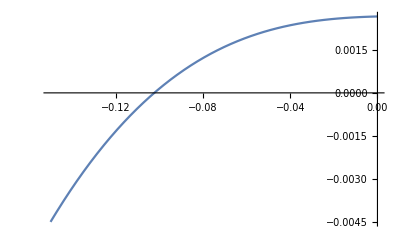

```mathematica
Plot[eq/.{θ->2.6},{dth,-0.15,0}]
```

```mathematica
Stress={};
```

```mathematica
dtn={};
```

```mathematica
step=0.01;
```

```mathematica
Do[soldth=FullSimplify[Solve[eq==0,dth,Assumptions->-0.14<dth<=0]];Pn=(4*c1/d3/Sqrt[Det[Aᵀ.A]]*(A.Aᵀ.A-A.Adᵀ.Ad-Inverse[Aᵀ]*Tr[(Aᵀ.A-Adᵀ.Ad).(Aᵀ.A-Adᵀ.Ad)]/4))/.soldth;dthn=dth/.soldth;AppendTo[dtn,dthn];AppendTo[Stress,Pn],{θ,0,2.61,step}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
nmax=2.61/step+1;
```

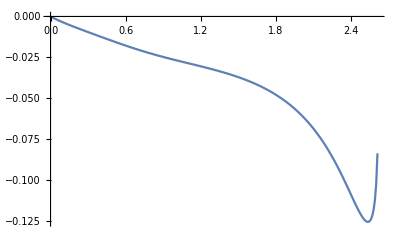

```mathematica
ListLinePlot[Table[{(n-1)*step,Flatten[dtn][[n]]},{n,nmax}],PlotRange->Full]
```

```mathematica
(*ListLinePlot[Table[{(n-1)*step,-Stress[[n]][[1]][[1,1]]},{n,2,nmax}]]*)
```

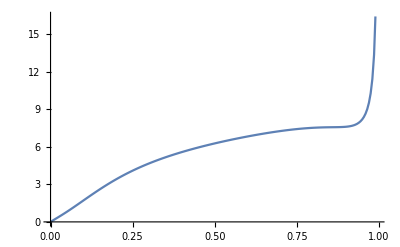

```mathematica
ListLinePlot[Table[{1-utm[(n-1)*step+ϕ]/utm[ϕ],-Stress[[n]][[1]][[1,1]]},{n,2,nmax}]]
```

```mathematica
(*ListLinePlot[Table[{(n-1)step,Stress[[n]][[1]][[2,2]]},{n,nmax}]]*)
```

```mathematica
(*ListLinePlot[Table[{(n-1)step,Norm[Stress[[n]][[1]],"Frobenius"]},{n,nmax}]]*)
```

#### Solving quadratic equation

```mathematica
a=3/2c1 gp;b=2c1 g + 2d3 J;c=2d3 J θ;
```

```mathematica
(*eq2= FullSimplify[2c1 Tr[(dth D[Aᵀ.A,θ]+ 3/2 dth^2 D[Aᵀ.A,{θ,2}]).D[Aᵀ.A,θ]]+2d3 θ]*)
```

```mathematica
eq2= a dth^2+b dth+c;
```

```mathematica
root1=(-b+√(b^2-4a c))/(2a);root2=(-b-√(b^2-4a c))/(2a);(*root1 works*)
```

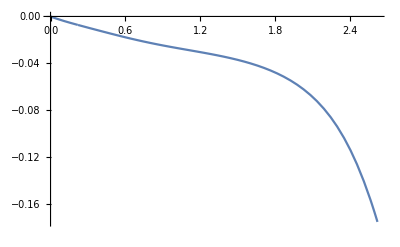

```mathematica
Plot[root1,{θ,0,ulim}]
```

```mathematica
Pnroot1=-4*c1/J*A.(Cp*root1+root1^2/2 * Cpp+Inverse[Aᵀ.A]*g root1^2/4);
```

```mathematica
(*Plot[{Pnroot1[[1,1]],Pnroot1[[2,2]],-Norm[Pnroot1,"Frobenius"]},{θ,0,1.5},ImageSize->Large,PlotLegends->"Expressions"]*)
```

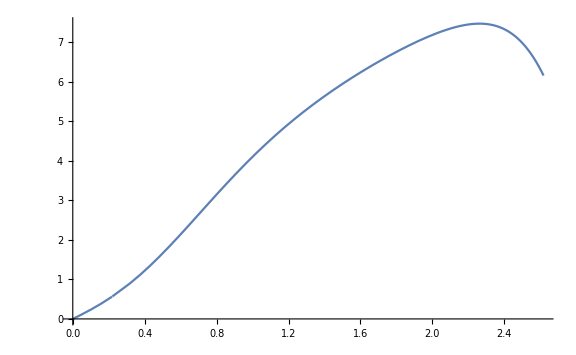

```mathematica
Plot[-Pnroot1[[1,1]]/d3,{θ,0,ulim},ImageSize->Large,PlotLegends->"Expressions"]
```

```mathematica
(*Plot[root2,{θ,0,1.5}]*)
```

```mathematica
(*Pnroot2=-4*c1*A.Cp*root2;*)
```

```mathematica
(*Plot[{Pnroot2[[1,1]],Pnroot2[[2,2]],Norm[Pnroot2,"Frobenius"]},{θ,0,1.5},ImageSize->Large,PlotLegends->"Expressions"]*)
```

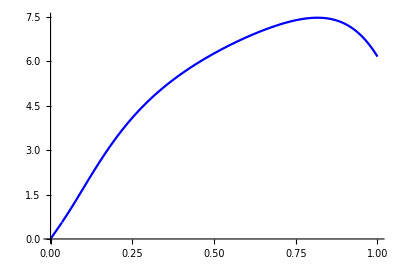

```mathematica
ParametricPlot[{1-utm[θ+ϕ]/utm[ϕ],-Pnroot1[[1,1]]/d3},{θ,0,ulim},AspectRatio->2/3,PlotStyle->{Blue},PlotLegends->"quadratic approximation"]
```

Paul’s formula

```mathematica
rootp=-2d3/c1 θ/g/(1+Sqrt[1-3d3/c1 θ gp/g^2]);
```

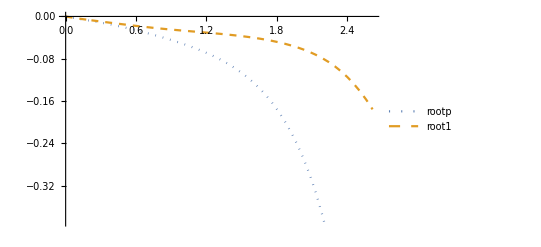

```mathematica
Plot[{rootp,root1},{θ,0,ulim},PlotLegends->"Expressions",PlotStyle->{Dotted,Dashed}]
```

#### Comparison to the FE Solution

```mathematica
DispForce=Import["/Users/hu/Desktop/Firedrake/Miura/2D/Hu/Mechanism/force/DispForce.csv","Data"];
```

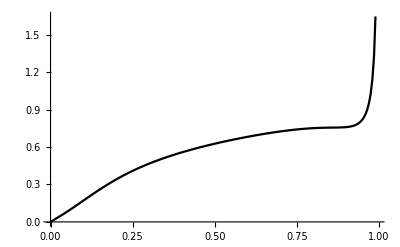

```mathematica
ListLinePlot[DispForce,PlotStyle->{Black},PlotLegends->"numerical simulation"]
```

```mathematica
(*Show[ParametricPlot[{1-utm[θ+ϕ]/utm[ϕ],-P[[1,1]]},{θ,0,1.5}],ParametricPlot[{1-utm[θ+ϕ]/utm[ϕ],-Pnroot1[[1,1]]},{θ,0,1.5}],ListLinePlot[DispForce],AspectRatio->1/GoldenRatio,ImageSize->Large]*)
```

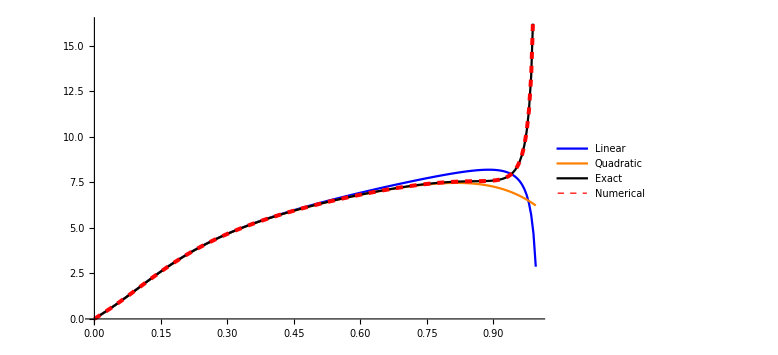

```mathematica
ListLinePlot[{Table[{1-utm[θ+ϕ]/utm[ϕ],-P[[1,1]]},{θ,0,2.61,step}],Table[{1-utm[θ+ϕ]/utm[ϕ],-Pnroot1[[1,1]]/d3},{θ,0,2.61,step}],Table[{1-utm[(n-1)*step+ϕ]/utm[ϕ],-Stress[[n]][[1]][[1,1]]},{n,2,nmax}],DispForce.{{1,0},{0,1/d3}}},PlotStyle->{Blue,Orange,Black,{Red,Dashed,Thickness[0.005]}},ImageSize->Large,PlotLegends->{"Linear","Quadratic","Exact","Numerical"}]
```

```mathematica
(*ListLinePlot[{Table[{1-utm[θ+ϕ]/utm[ϕ],-P[[1,1]]/d3},{θ,0,2.61,step}],Table[{1-utm[θ+ϕ]/utm[ϕ],-Pnroot1[[1,1]]/d3},{θ,0,2.61,step}],Table[{1-utm[(n-1)*step+ϕ]/utm[ϕ],-Stress[[n]][[1]][[1,1]]/d3},{n,2,nmax}]},PlotStyle->{Blue,Orange,Black,{Red,Dashed,Thickness[0.005]}},ImageSize->Large,PlotLegends->{"Linear","Quadratic","Nonelinear"}]*)
```